```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants.txt","CSV"];
```

```mathematica
dataSeedBank=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants_seedbank_strength_1herb_10no.txt","CSV"];
```

## Extinction probabilities and standing variation

### Extinction probabilities of the plant lineages

#### Parameters of the model

```mathematica
b=0.9 140;
dZ=0.35;
gZ = 0.2;
p=0.95;
f=0.9 13000;
dS=0.94;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
g = 0.3;
dB=0.48;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
densSeeds=80;
densPlants=1;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[[j]]/(1-β);
Γ[i_]:=Exp[Sum[λm[i,j](γ[[j]]/(1-β)-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities for lineages generated by the different plant genotypes

```mathematica
q={q1,q2,q3}/.FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet
```

{0.999964,8.64296×10^-66,1.34674×10^-109}

#### Extinction probabilities for lineages generated by the different seed genotypes

```mathematica
qm={(α[[1]]q[[1]]+γ[[1]])/(1-β),(α[[2]]q[[2]]+γ[[2]])/(1-β),(α[[3]]q[[3]]+γ[[3]])/(1-β)}
```

{1.,0.877113,0.754717}

### Standing genetic variation in untreated population

#### Standing genetic variation for a self-pollinating population

```mathematica
Clear[c];
p=1;
```

```mathematica
pos1=Flatten[Position[dataStandingVariation⟦All,1⟧,p]];
```

#### Standing genetic variation for a cross-pollinating population

```mathematica
p=0;
```

```mathematica
pos2=Flatten[Position[dataStandingVariation⟦All,1⟧,p]];
```

#### Standing genetic variation as a function of the resistance cost

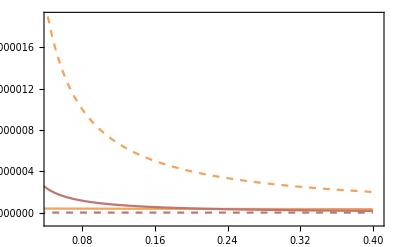

```mathematica
Show[ListPlot[Table[Partition[Riffle[dataStandingVariation[[pos1,2]],dataStandingVariation[[pos1,i]]],2],{i,4,5}],DataRange->{0.05,0.4},PlotRange->{{0.045,0.405},{-9 10^-8,1.9 10^-6}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->{RGBColor["#F2A35E"],RGBColor["#BF766F"]},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None],ListPlot[Table[Partition[Riffle[dataStandingVariation[[pos2,2]],dataStandingVariation[[pos2,i]]],2],{i,4,5}],DataRange->{0.05,0.4},PlotRange->{{0.045,0.405},{-9 10^-8,1.9 10^-6}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->{Directive[Dashed,RGBColor["#F2A35E"]],Directive[Dashed,RGBColor["#BF766F"]]},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None]]
```

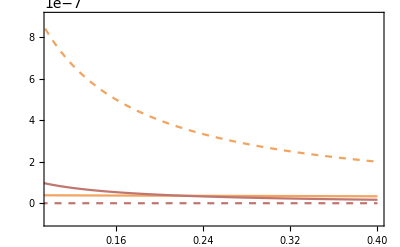

```mathematica
Show[ListPlot[Table[Partition[Riffle[dataStandingVariation[[pos1,2]],dataStandingVariation[[pos1,i]]],2],{i,4,5}],DataRange->{0.1,0.4},PlotRange->{{0.1,0.4},{-9 10^-8,9 10^-7}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->{RGBColor["#F2A35E"],RGBColor["#BF766F"]},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None],ListPlot[Table[Partition[Riffle[dataStandingVariation[[pos2,2]],dataStandingVariation[[pos2,i]]],2],{i,4,5}],DataRange->{0.1,0.4},PlotRange->{{0.1,0.4},{-9 10^-8,9 10^-7}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->{Directive[Dashed,RGBColor["#F2A35E"]],Directive[Dashed,RGBColor["#BF766F"]]},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None]]
```

### Seed bank composition of pre-treated population

#### Standing genetic variation for a self-pollinating population

```mathematica
Clear[c];
p=1;
```

```mathematica
pos1=Flatten[Position[dataStandingVariation⟦All,1⟧,p]];
```

#### Standing genetic variation for a cross-pollinating population

```mathematica
p=0;
```

```mathematica
pos2=Flatten[Position[dataStandingVariation⟦All,1⟧,p]];
```

#### Standing genetic variation as a function of the resistance cost

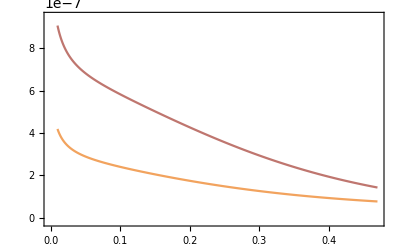

```mathematica
ListPlot[Table[Partition[Riffle[dataSeedBank[[All,1]],dataSeedBank[[All,i]]],2],{i,4,5}],PlotRange->{Automatic,{-2 10^-8,9.5 10^-7}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->{RGBColor["#F2A35E"],RGBColor["#BF766F"]},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None]
```